# donald trump raman cooling simulation

sketchy part:
to get ABSB -- 
ARSB/ABSB = 1 + 1/nbar <--standard formula to get sideband asymmetry from temp
ABSB +ARSB = 1

This assumes that the raman NEVER heats. ie that RP is strong enough that as soon as atom makes  a pi transition, it gets repumped back to F4. In real life, you cannot turn down RP aribtrarily because it has to keep up with the raman rabi rate to prevent >pi pulses. However in this simulation you cna turn it down arbitrarily and it will keep returning an ever lower final temperature. so beware of that.

## actual parameters:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{nbar→0.0452526}}

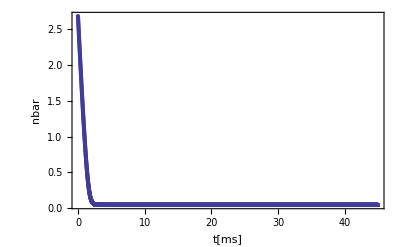
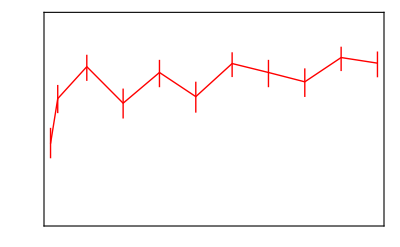

```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]
kHz=1 10^3;
ms=10^-3;
us=10^-6;
nm=1 10^-9;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
polPurity=500; (*measured ratio of OP depumping rates in misaligned vs aligned B field*)

ROP=1/(20 us);(*measured repumping scattering rate.*)

ΩBSB=(2π)/(2 100 us); (*estimated by eye from the crappy sideband rabi flop*)
frad=80 kHz; (*measured and fitted radial sidebands*)
λOP=852nm;

ABSB=1/(1/nbar+2); (*empirically seems to be the case, not really based on physics.*)
Rcool=-ABSB ΩBSB/(2π) ℏ 2π frad/kB; (*cooling rate sitting on cooling SB*)
Rheat=ROP/polPurity ℏ (2π)/λOP/kB; (*heating rate due to wrong polarization components in RP*)

Solve[Rcool+Rheat==0,nbar]
Clear[nbar]
nt=Reap[
Δt=.01ms;
nbar=2.7;
Do[
nbar=nbar+(Rcool+Rheat)/((ℏ 2π frad)/kB)Δt;
(*denominator converts temperature to nbar*)
Sow[{n Δt/ms,nbar,Rcool+Rheat}]
,{n,0,Round[45ms/Δt]}]
][[2,1]];
(*from: tweezer scans/2016/3_31/test14*)
survival=
{{{0.01,0.38095238095238093},ErrorBar[{-0.07133967666990054,0.07687677523025488}]},{{1.,0.6},ErrorBar[{-0.07058823529411765,0.06666666666666667}]},{{5.,0.7555555555555555},ErrorBar[{-0.06916289569650746,0.058051784585396615}]},{{10.,0.5777777777777777},ErrorBar[{-0.07453403072199638,0.0711523882099192}]},{{15.,0.7272727272727273},ErrorBar[{-0.07163294342495763,0.06153193332394746}]},{{20.,0.6097560975609756},ErrorBar[{-0.07792851713926274,0.07270203630302585}]},{{25.,0.7708333333333334},ErrorBar[{-0.06582346224910152,0.05476904048039399}]},{{30.,0.7272727272727273},ErrorBar[{-0.07163294342495763,0.06153193332394746}]},{{35.,0.6818181818181818},ErrorBar[{-0.07359082822263441,0.06551002014182639}]},{{40.,0.8},ErrorBar[{-0.06585801766937471,0.05281453940850511}]},{{45.,0.7727272727272727},ErrorBar[{-0.06882519750669092,0.05670398538547872}]}};

Overlay[{
ListPlot[nt[[;;,{1,2}]],PlotRange->All,Axes->False,Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic},FrameLabel->{"t[ms]","nbar","Raman cooling simulation vs data",None},ImagePadding->{{40,40},{40,15}}],
ErrorListPlot[survival,Joined->True,PlotStyle->{Thick,Red},Frame->{False,False,False,True},FrameTicks->{None,None,None,All},FrameStyle->{Automatic,Automatic,Automatic,Red},PlotRange->{All,{0,1}},FrameLabel->{None,None,None,"survival prob"},
ImagePadding->{{40,40},{40,15}}]
}]
```

## change params..

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{nbar→0.710227}}

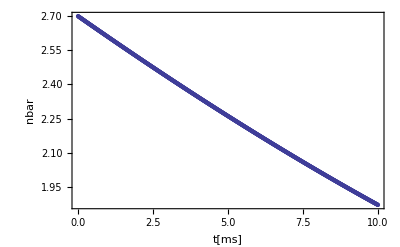

```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]
kHz=1 10^3;
ms=10^-3;
us=10^-6;
nm=1 10^-9;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
polPurity=500; (*measured ratio of OP depumping rates in misaligned vs aligned B field*)

ROP=1/(20 us); (*measured repumping scattering rate.*)

ΩBSB=(2π)/(2 100 us); (*estimated by eye from the crappy sideband rabi flop*)
frad=80 kHz; (*measured and fitted radial sidebands*)
λOP=852nm;

ABSB=1/(1/nbar+2); (*empirically seems to be the case, not really based on physics.*)
Rcool=-ABSB ΩBSB/(2π) ℏ 2π frad/kB; (*cooling rate sitting on cooling SB*)
Rheat=ROP/polPurity ℏ (2π)/λOP/kB; (*heating rate due to wrong polarization components in RP*)

Solve[Rcool+Rheat==0,nbar]
Clear[nbar]
nt=Reap[
Δt=.01ms;
nbar=2.7;
Do[
nbar=nbar+(Rcool+Rheat)/((ℏ 2π frad)/kB)Δt;
(*denominator converts temperature to nbar*)
Sow[{n Δt/ms,nbar,Rcool+Rheat}]
,{n,0,Round[10ms/Δt]}]
][[2,1]];
(*from: tweezer scans/2016/3_31/test14*)
survival=
{{{0.01,0.38095238095238093},ErrorBar[{-0.07133967666990054,0.07687677523025488}]},{{1.,0.6},ErrorBar[{-0.07058823529411765,0.06666666666666667}]},{{5.,0.7555555555555555},ErrorBar[{-0.06916289569650746,0.058051784585396615}]},{{10.,0.5777777777777777},ErrorBar[{-0.07453403072199638,0.0711523882099192}]},{{15.,0.7272727272727273},ErrorBar[{-0.07163294342495763,0.06153193332394746}]},{{20.,0.6097560975609756},ErrorBar[{-0.07792851713926274,0.07270203630302585}]},{{25.,0.7708333333333334},ErrorBar[{-0.06582346224910152,0.05476904048039399}]},{{30.,0.7272727272727273},ErrorBar[{-0.07163294342495763,0.06153193332394746}]},{{35.,0.6818181818181818},ErrorBar[{-0.07359082822263441,0.06551002014182639}]},{{40.,0.8},ErrorBar[{-0.06585801766937471,0.05281453940850511}]},{{45.,0.7727272727272727},ErrorBar[{-0.06882519750669092,0.05670398538547872}]}};


ListPlot[nt[[;;,{1,2}]],PlotRange->All,Axes->False,Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic},FrameLabel->{"t[ms]","nbar","Raman cooling simulation vs data",None},ImagePadding->{{40,40},{40,15}}]
```

```mathematica
1. (2 100 us)/(√2)/us
```

141.421

```mathematica
1/(20 us)
```

50000

```mathematica
1. (√2)/(2 100 us)
```

7071.07

```mathematica
1. 50000/7071
```

7.07114